# Chapter :: 19 Numerics In General

## Loss Of Significant Digits Quadratic Equation:

```mathematica
Clear[a,b,c,x]
```

```mathematica
eq = a x^2 + b x + c ==0
```

c+b x+a x^2==0

```mathematica
sol= Solve[eq,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Sol ={sol[[1,1,2]],sol[[2,1,2]]}/.{a ->1,b->-40,c->2}
```

{1/2 (40-2 √398),1/2 (40+2 √398)}

```mathematica
x2 =N[Sol[[2]],4]
```

39.95

```mathematica
x1 =(2/1)/x2
```

0.05006

```mathematica
N[Sol[[1]],4]
```

0.05006

```mathematica
x2b =N[Sol[[2]],30]
```

39.9499373432600033316538822341

```mathematica
40-x2b
```

0.0500626567399966683461177659

```mathematica
2/x2b
```

0.0500626567399966683461177658615

```mathematica
N[Sol[[1]],30]
```

0.0500626567399966683461177658615

## Fixed-Point Iteration::

```mathematica
(* x^3 + x -1 =0 *)
```

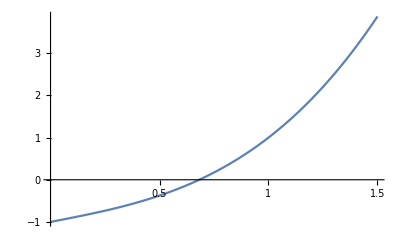

```mathematica
Plot[x^3 +x -1,{x,0,1.5},Ticks->{{0.5,1,1.5},Automatic}]
```

```mathematica
Clear[x]
```

```mathematica
x[0] =1
```

1

```mathematica
g[x_] =1/(1+x^2)
```

1/(1+x^2)

```mathematica
Do[x[n] =N[g[x[n-1]]],{n,1,30}]
```

```mathematica
Table[x[n],{n,0,30}]
```

{1,0.5,0.8,0.609756,0.728968,0.653,0.701061,0.670472,0.689878,0.677538,0.685374,0.680394,0.683557,0.681547,0.682824,0.682013,0.682528,0.682201,0.682409,0.682276,0.68236,0.682307,0.682341,0.682319,0.682333,0.682324,0.68233,0.682326,0.682329,0.682327,0.682328}

```mathematica
N[Solve[x^3 +x == 1,x]]
```

{{x→0.682328},{x→-0.341164-1.16154 ⅈ},{x→-0.341164+1.16154 ⅈ}}

```mathematica
P1 = Plot[x,{x,0,1}];
```

```mathematica
P2 = Plot[g[x],{x,0,1.5}];
```

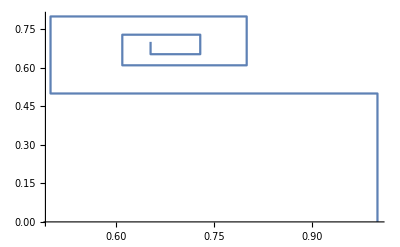

```mathematica
P3 = ListPlot[{{x[0],0},{x[0],x[1]},{x[1],x[1]},{x[1],x[2]},{x[2],x[2]},{x[2],x[3]},{x[3],x[3]},{x[3],x[4]},{x[4],x[4]},{x[4],x[5]},{x[5],x[5]},{x[5],x[6]}},
PlotJoined ->True]
```

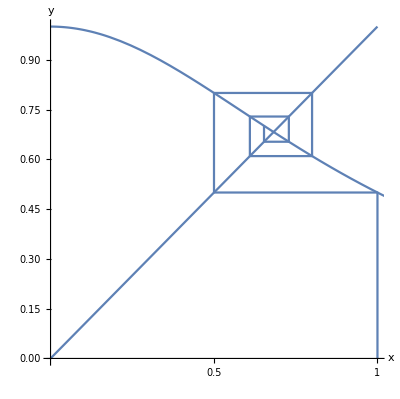

```mathematica
Show[{P1,P2,P3},AspectRatio->Automatic,AxesLabel->{x,y},Ticks->{{0.5,1,1.5},Automatic}]
```

## Solving Equations By Newton’s Method::

```mathematica
(* 2sinx=x *)
```

```mathematica
f = x-2Sin[x]
```

x-2 Sin[x]

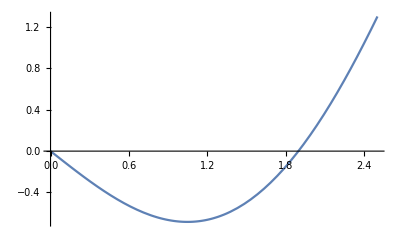

```mathematica
Plot[f,{x,0,2.5}]
```

```mathematica
g[x_] =f/D[f,x]
```

(x-2 Sin[x])/(1-2 Cos[x])

```mathematica
x[0]=2
```

2

```mathematica
Do[x[n]=N[x[n-1]-g[x[n-1]]],{n,1,6}]
```

```mathematica
S =Table[x[n],{n,0,6}]
```

{2,1.901,1.89551,1.89549,1.89549,1.89549,1.89549}

```mathematica
f/.x-> S[[4]]
```

2.86219×10^-10

```mathematica
Clear[x]
```

```mathematica
FindRoot[f==0,{x,2}]
```

{x→1.89549}

## Solving Equations By The Secant Method:

```mathematica
(* Solve  f(x) =x-2sinx=0 *)
```

```mathematica
Clear[x,f]
```

```mathematica
f[x_]=x-2Sin[x]
```

x-2 Sin[x]

```mathematica
x[0]=2
```

2

```mathematica
x[1]=1.8
```

1.8

```mathematica
Do[
x[n+1]=x[n]-N[f[x[n]](x[n]-x[n-1])/(f[x[n]]-f[x[p-1]])],{n,1,8}]
```

```mathematica
Table[x[n],{n,1,8}]
```

## Solving Equations By The Bisection Method Module::

```mathematica
bisect[f_,a_,b_,acc_] := Module[{left,right,mid,n},{ left =a; right =b;
n = Ceiling[N[Log[(b-a)/acc]/Log[2]]]; mid =N[(a+b)/2];
Do[If[N[(f[x]/.x->left) (f[x]/.x->mid)]>0, left=mid,
right =mid]; mid =N[(left +right)/2],{j,i,n}]
};Return[mid]]
```

```mathematica
||bisect.m
```

## Polynomial Interploation

```mathematica
u ={9,9.5,11}
```

{9,9.5,11}

```mathematica
v ={2.1972,2.2513,2.3979}
```

{2.1972,2.2513,2.3979}

```mathematica
InterpolatingPolynomial[{{u[[1]],v[[1]]},{u[[2]],v[[2]]},{u[[3]],v[[3]]}},x]
```

2.3979+(0.10035-0.00523333 (-9+x)) (-11+x)

```mathematica
Expand[%]
```

0.77595+0.205017 x-0.00523333 x^2

```mathematica
%/.x->9.2
```

2.21915

```mathematica
seq =Table[{u[[j]],v[[j]]},{j,1,3}]
```

{{9,2.1972},{9.5,2.2513},{11,2.3979}}

```mathematica
InterpolatingPolynomial[seq,x]
```

2.3979+(0.10035-0.00523333 (-9+x)) (-11+x)

```mathematica
Expand[%]
```

0.77595+0.205017 x-0.00523333 x^2

```mathematica
al1 =(v[[2]]-v[[1]])/(u[[2]]-u[[1]])
```

0.1082

```mathematica
al2 =(v[[3]]-v[[2]])/(u[[3]]-u[[2]])
```

0.0977333

```mathematica
a21 =(al2-al1)/(u[[3]]-u[[1]])
```

-0.00523333

```mathematica
p =v[[1]]+(x-u[[1]])al1+(x-u[[1]])(x-u[[2]])a21
```

2.1972+0.1082 (-9+x)-0.00523333 (-9.5+x) (-9+x)

```mathematica
Expand[%]
```

0.77595+0.205017 x-0.00523333 x^2

## Spline Interpolation::

```mathematica
u1 ={-4,-3,-2,-1,0,1,2,3,4}
```

{-4,-3,-2,-1,0,1,2,3,4}

```mathematica
v1 ={0,0,0,0,1,0,0,0,0}
```

{0,0,0,0,1,0,0,0,0}

```mathematica
w =Table[{u1[[j]],v1[[j]]},{j,1,9}]
```

{{-4,0},{-3,0},{-2,0},{-1,0},{0,1},{1,0},{2,0},{3,0},{4,0}}

```mathematica
p1 =InterpolatingPolynomial[v1,x]
```

(1/24+(-1/24+(1/48+(-1/144+1/576 (-8+x)) (-7+x)) (-6+x)) (-5+x)) (-4+x) (-3+x) (-2+x) (-1+x)

```mathematica
Expand[%]
```

126-(1325 x)/4+(5455 x^2)/16-(26365 x^3)/144+(32773 x^4)/576-(1525 x^5)/144+(335 x^6)/288-(5 x^7)/72+x^8/576

```mathematica
N[%]
```

126.-331.25 x+340.938 x^2-183.09 x^3+56.8976 x^4-10.5903 x^5+1.16319 x^6-0.0694444 x^7+0.00173611 x^8

```mathematica
p4 =ListPlot[w,Prolog->AbsolutePointSize[4]];
```

```mathematica
p5 =Plot[p1,{x,-4,4}];
```

```mathematica
Show[p4,p5]
```

-Graphics-

```mathematica
Needs["Splines`"]
```

```mathematica
spline=SplineFit[w,Cubic]
```

SplineFit[w,Cubic]

```mathematica
spline[0]
```

SplineFit[w,Cubic][0]

```mathematica
spline[0.5]
```

SplineFit[w,Cubic][0.5]

## Numeric Integration

```mathematica
Clear[f]
```

```mathematica
f[x_] =Exp[-x^2]
```

ⅇ^(-x^2)

```mathematica
a =0; b=1;M=10 ;h=(b-a)/M;
```

```mathematica
RectRule =h(Sum[f[x],{x,a+h/2,b-h/2,h}])
```

1/10 (1/ⅇ^(361/400)+1/ⅇ^(289/400)+1/ⅇ^(9/16)+1/ⅇ^(169/400)+1/ⅇ^(121/400)+1/ⅇ^(81/400)+1/ⅇ^(49/400)+1/ⅇ^(1/16)+1/ⅇ^(9/400)+1/ⅇ^(1/400))

```mathematica
N[%]
```

0.747131

```mathematica
TrapezRule =h(f[a]/2 +f[b]/2+Sum[f[x],{x,a+h,b-h,h}])
```

1/10 (1/2+1/(2 ⅇ)+1/ⅇ^(81/100)+1/ⅇ^(16/25)+1/ⅇ^(49/100)+1/ⅇ^(9/25)+1/ⅇ^(1/4)+1/ⅇ^(4/25)+1/ⅇ^(9/100)+1/ⅇ^(1/25)+1/ⅇ^(1/100))

```mathematica
N[%]
```

0.746211

```mathematica
SimpsonRule =h/3(f[a]+4Sum[f[x],{x,a+h,b-h,2h}]+2Sum[f[x],{x,a+2h,b-2h,2h}]+f[1])
```

1/30 (1+2 (1/ⅇ^(16/25)+1/ⅇ^(9/25)+1/ⅇ^(4/25)+1/ⅇ^(1/25))+4 (1/ⅇ^(81/100)+1/ⅇ^(49/100)+1/ⅇ^(1/4)+1/ⅇ^(9/100)+1/ⅇ^(1/100))+1/ⅇ)

```mathematica
N[%]
```

0.746825

```mathematica
1/2(5/9 Exp[-1/4(-Sqrt[3/5]+1)^2]+8/9 Exp[-1/4]+5/9Exp[-1/4(Sqrt[3/5]+1)^2])
```

1/2 (8/(9 ⅇ^(1/4))+5/9 ⅇ^(-1/4 (1-√(3/5))^2)+5/9 ⅇ^(-1/4 (1+√(3/5))^2))

```mathematica
N[%]
```

0.746815

```mathematica
(*Done )
```